```mathematica
ClearAll["Global`*"]
```

```mathematica
FlipFlop[n_,i_,j_]:=Block[
{v=IntegerDigits[n,2,L]},
If[v[[i]]≠0&&v[[j]]≠1,
v[[i]]=v[[i]]-1;
v[[j]]=v[[j]]+1;
FromDigits[v,2]
,
-1]
]
Raise[n_,i_]:=Block[
{v=IntegerDigits[n,2,L]},
If[v[[Mod[i,L,1]]]≠1,
v[[i]]=v[[i]]+1;
FromDigits[v,2]
,
-1]
]
U[t_,e_,v_]:=Transpose[v].DiagonalMatrix[Exp[-ⅈ e t]].Conjugate[v]
```

```mathematica
L=5;
```

```mathematica
Id=IdentityMatrix[2^L];
Heis=Table[
SparseArray[
Flatten@Table[
Block[{h=FlipFlop[j,i,k],v=2IntegerDigits[j,2,L]-1},
If[h≠-1,
{{j+1,h+1}->2.,
{h+1,j+1}->2.,
{j+1,j+1}->N[v[[i]]*v[[k]]]},
{{j+1,j+1}->N[v[[i]]*v[[k]]]}]
]
,{j,0,2^L-1}]
,{2^L,2^L}]
,{i,1,L},{k,1,L}];

Z2 = Table[
SparseArray[
Flatten@Table[
Block[{h=FlipFlop[j,i,k],v=2IntegerDigits[j,2,L]-1},
{j+1,j+1}-> N[v[[i]]*v[[k]]]
]
,{j,0,2^L-1}]
,{2^L,2^L}]
,{i,1,L},{k,1,L}];

Sz=Monitor[Table[
SparseArray[
Table[
Block[{v=2IntegerDigits[j,2,L]-1},
{j+1,j+1}->N[v[[i]]]
]
,{j,0,2^L-1}]
,{2^L,2^L}]
,{i,1,L}],i];
SzTot=Sum[Sz[[i]],{i,L}];



Sp=Monitor[Table[
SparseArray[
DeleteCases[Table[
Block[{h=Raise[j,i]},
If[h≠-1,
{h+1,j+1}->1.]
]
,{j,0,2^L-1}]
,Null]
,{2^L,2^L}]
,{i,1,L}],i];
Sm=Monitor[Table[Transpose[Sp[[i]]]
,{i,1,L}],i];
Sx = Table[Sp[[i]]+Sm[[i]],{i,1,L}];
```

```mathematica
IntegerDigits[#,2,L]&/@(Range[2^L]-1)
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

## Exact time evolution

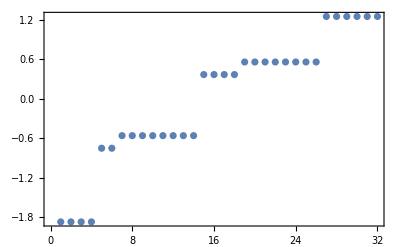

```mathematica
H=(Sum[Heis[[i,Mod[i+1,L,1]]],{i,1,L}])/4;
(*H  =(Sum[Heis[[i,Mod[i+1,L,1]]],{i,1,L}] + Sum[Z2[[i,Mod[i+2,L,1]]],{i,1,L}]) /4;)*)
{e,v}=Eigensystem[H];
eigs=e[[Ordering[e]]];
vecs=v[[Ordering[e]]];
ListPlot[Chop@eigs,Frame->True]
```

```mathematica
Chop[vecs[[1]]]
```

{0,0,0,0.204322,0,-0.288654,-0.0259239,-0.0119265,0,-0.0678697,0.39847,0,-0.220344,0.0312241,-0.0192975,0,0,0.152202,-0.576868,0.0119265,0.534922,-0.0505216,0.0505216,0,-0.110256,0.0192975,-0.0312241,0,0,0,0,0}

```mathematica
tf=50(*/Jp*);
dt=tf/200;
Nt=IntegerPart[tf/dt];
```

```mathematica
c=Table[(1+(-1)^i)/2,{i,L}];
init=UnitVector[2^L,FromDigits[c,2]]
```

{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
AbsoluteTiming[
(*u=U[dt,eigs,vecs];*)
revos=ConstantArray[0,Nt+1];
revos[[1]]=init;
Monitor[Do[
(*revos[[i+1]]=u.revos[[i]];*)
revos[[i+1]]=MatrixExp[-ⅈ(dt)H,revos[[i]]];
,{i,1,Nt}],i];
]
Szt=Table[{(t-1)dt,Conjugate[revos[[t]]].(Sx[[1]].Sz[[2]].Sz[[3]].Sx[[4]]).revos[[t]]/2},{t,1,Length@revos}];
```

{0.163627,Null}

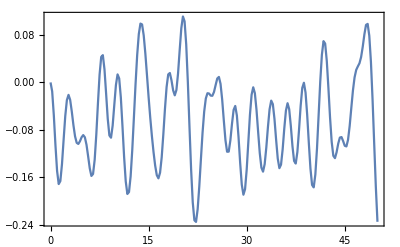

```mathematica
ListPlot[Szt,Frame->True,Joined->True,PlotRange->All]
```

## Trotter Evolution

```mathematica
TrotterEvolve[tf_,nt_,init_]:=Block[
{dt=N[tf/nt],UOdd,UEven,UTrotter,ψtrot},
UOdd=MatrixExp[-ⅈ dt Sum[Heis[[i,Mod[i+1,L,1]]],{i,1,L,2}]/4];
UEven=MatrixExp[-ⅈ dt Sum[Heis[[i,Mod[i+1,L,1]]],{i,2,L,2}]/4];
UTrotter=UEven.UOdd;
ψtrot={init};
Do[
AppendTo[ψtrot,UTrotter.ψtrot[[-1]]];
,{t,1,nt}];
ψtrot[[-1]]
]
```

```mathematica
TrotterFixStepList={init};
Do[
AppendTo[TrotterFixStepList,TrotterEvolve[n*dt,10,init]],
{n,1,Nt}]
TrotterFixStepSz=Table[{(t-1)dt,Conjugate[TrotterFixStepList[[t]]].Sz[[1]].TrotterFixStepList[[t]]/2},{t,1,Length@TrotterFixStepList}];
```

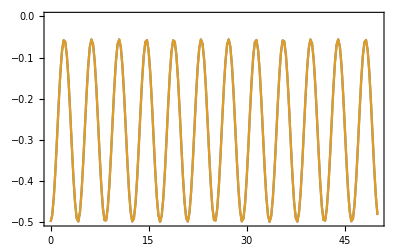

```mathematica
ListPlot[{Szt,TrotterFixStepSz},Joined->True,Frame->True]
```

## Ansatz

```mathematica
p = 1;
foo[θSeq___]:=With[{θ={θSeq}},
Dot[Sequence@@Reverse[Table[Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[(i*L)+n]]Heis[[n,Mod[n+1,L,1]]]],{n,2,L,2}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[(i*L)+n]]Heis[[n,Mod[n+1,L,1]]]],{n,1,L,2}]]]
,{i,0,p-1}]]].init
]
vars=ToExpression[Table["θ"<>ToString[n],{n,1,p*L}]]
```

{θ1,θ2,θ3}

```mathematica
(*Timing[Mean[Table[FindMinimum[1-Abs[Conjugate[revos[[-1]]].foo[Sequence@@vars]],Partition[Riffle[vars,RandomReal[{0,2π},Length@vars]],2]][[1]],1]]]*)
Timing[Mean[Table[FindMinimum[Abs[Conjugate[revos[[-1]]].(Sx[[2]].Sx[[3]].Sx[[4]].Sx[[5]]).revos[[-1]]/2 - Conjugate[foo[Sequence@@vars]].(Sx[[2]].Sx[[3]].Sx[[4]].Sx[[5]]).foo[Sequence@@vars]/2],Partition[Riffle[vars,RandomReal[{0,2π},Length@vars]],2]][[1]],1]]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.5,0.138733}

```mathematica
Monitor[varSzList=Table[{(t-1)dt,Block[{sol,bar},sol=FindMinimum[Abs[Conjugate[TrotterFixStepList[[t]]].Sz[[1]].TrotterFixStepList[[t]]/2 - Conjugate[foo[Sequence@@vars]].Sz[[1]].foo[Sequence@@vars]/2],Partition[Riffle[vars,RandomReal[{0,2π},Length@vars]],2]][[2]]; bar=foo[Sequence@@vars]/.sol;
Conjugate[bar].Sz[[1]].bar/2]},{t,1,Length@revos}];,t]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

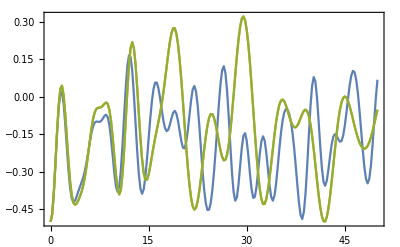

```mathematica
ListPlot[{Szt,TrotterFixStepSz, varSzList},Frame->True,PlotRange->All,Joined->True]
```